# Diffusion coefficients in orbital space

## Import data

```mathematica
tabaj=Import["../../data/Dump_Diffusion_Coefficients.hf5",{"Datasets","tabaj"}];
tabDRRjj=Import["../../data/Dump_Diffusion_Coefficients.hf5",{"Datasets","tabDRRjj"}]; 
tabDNRjj=Import["../../data/Dump_Diffusion_Coefficients.hf5",{"Datasets","tabDNRjj"}]; 
tabDjj=Import["../../data/Dump_Diffusion_Coefficients.hf5",{"Datasets","tabDjj"}]; 
tabaj={tabaj[[All,2]],tabaj[[All,1]]}//Transpose;
DRRjjTable=Partition[{tabaj,tabDRRjj}//Transpose//Flatten,3];
DNRjjTable=Partition[{tabaj,tabDNRjj}//Transpose//Flatten,3];
DjjTable=Partition[{tabaj,tabDjj}//Transpose//Flatten,3];
```

## Plot data

### SRR coefficients

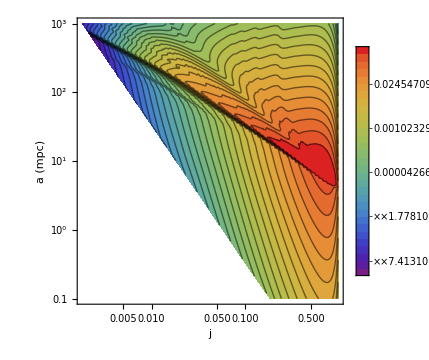

```mathematica
pRRjj=ListContourPlot[DRRjjTable,Contours->30,PlotRange->{All,All,All},ScalingFunctions->{"Log10","Log10","Log10"},ColorFunction->"Rainbow",PlotLegends->Automatic,Frame->True,AspectRatio->1,ImageSize->Medium,FrameLabel->{Style["j",Medium,Bold],Style["a (mpc)",Medium,Bold]}]
```

### NR diffusion coefficients

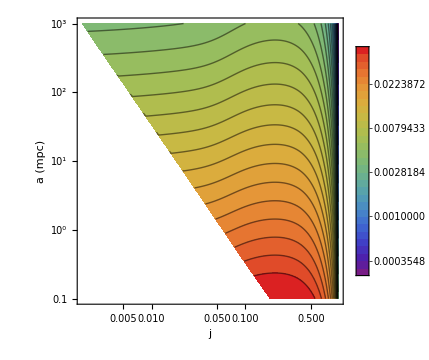

```mathematica
pNRjj=ListContourPlot[DNRjjTable,Contours->30,PlotRange->{All,All,All},ScalingFunctions->{"Log10","Log10","Log10"},ColorFunction->"Rainbow",PlotLegends->Automatic,Frame->True,AspectRatio->1,ImageSize->Medium,FrameLabel->{Style["j",Medium,Bold],Style["a (mpc)",Medium,Bold]}]
```

### Total diffusion coefficients

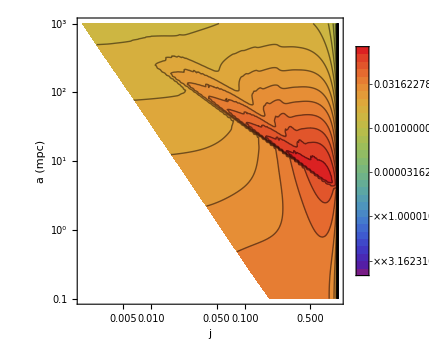

```mathematica
pjj=ListContourPlot[DjjTable,Contours->30,PlotRange->{All,All,All},ScalingFunctions->{"Log10","Log10","Log10"},ColorFunction->"Rainbow",PlotLegends->Automatic,Frame->True,AspectRatio->1,ImageSize->Medium,FrameLabel->{Style["j",Medium,Bold],Style["a (mpc)",Medium,Bold]}]
```

## Save data

### SRR diffusion coefficients

```mathematica
Export["../../graphs/Mathematica/DRRjj.png",pRRjj]
```

../../graphs/Mathematica/DRRjj.png

### NR diffusion coefficients

```mathematica
Export["../../graphs/Mathematica/DNRjj.png",pNRjj]
```

../../graphs/Mathematica/DNRjj.png

### Total diffusion coefficients

```mathematica
Export["../../graphs/Mathematica/Djj.png",pjj]
```

../../graphs/Mathematica/Djj.png